```mathematica
f[x_] = 26x^3 - 57x^2-41x+102
```

102-41 x-57 x^2+26 x^3

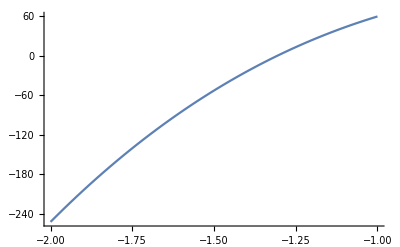

```mathematica
Plot[f[x], {x, -2, -1}]
```

```mathematica
a=-2;
b=-1;
epsilon=0.001;

c=a-f[a] (b-a)/(f[b]-f[a]);
fc=f[c];
i = 1;

While[Abs[fc]>epsilon,
If [fc f[b]>0,
b=c;
fb=fc;
,
a=c;
fa=fc;
 ];

c=a-f[a] (b-a)/(f[b]-f[a]);
fc=f[c];
i++];

N[c,3]
i
```

-1.31

11

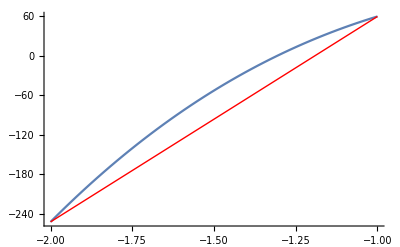

```mathematica
a=-2;
b=-1;
fa=f[a];
fb=f[b];
c1=a-fa (b-a)/(fb-fa);
fc1=f[c1];
Show[Plot[f[x],{x,a,b}],Graphics[{Red,Line[{{a,fa},{b,fb}}]}]]
```

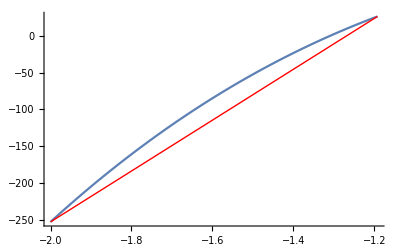

```mathematica
If [fc f[b]>0,
b=c1;
,
a=c1;
 ];
fa=f[a];
fb=f[b];
c2=a-fa (b-a)/(fb-fa);
fc2=f[c2];
Show[Plot[f[x],{x,a,b}],Graphics[{Red,Line[{{a,fa},{b,fb}}]}]]
```